```mathematica
(*Load the Josh 2.0 library for every new *)
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
pos={0.09625,-78.0387}
(*At 70 --> 1.38012291979976*)
```

TEMPERATURE CONTROLLER CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
TempCtrlOff[]
```

0

```mathematica
TempCtrlInit[]
```

0

```mathematica
TempCtrlOn[]
```

0

```mathematica
TempCtrlPlotTemp[90,2]
```

TempCtrlPlotTemp[90,2]

```mathematica
TempCtrlSetSetpoint[90]
```

90.

```mathematica
TempCtrlGetTemp[]
```

76.19

BATH CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
BathOff[]
```

0

```mathematica
BathInit[]
```

0

```mathematica
BathOn[]
```

0

```mathematica
BathGetTemp[]
```

30.1

```mathematica
BathGetSetpoint[]
```

90.

```mathematica
BathSetSetpoint[30]
```

30.

SERVO CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
ServoDisable[]
```

0

```mathematica
ServoReady[]
```

0

```mathematica
ServoEnable[]
```

0

```mathematica
ServoHomed[]
```

ServoHomed[]

```mathematica
ServoHome[5000]
```

0

```mathematica
ServoGetPos[]
```

{0.09625,-78.0387}

```mathematica
ServoManualControl[]
```

0

LABJACK CONTROLS

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]]
Needs["WolframMachineControl`"]
```

{C:\Users\Student\Desktop\machine_controller\MachineControl\v2}

```mathematica
ReadLabjack[3]
```

0.128796

```mathematica
LabJackRecordData["monopalmatin_60_3",20,3]
```

Recorded 1201 readings over 3961 s -- saved to C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_60_3.csv

C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_60_3.csv

```mathematica
LabJackListCSVs[]
```

File Name | Date Created
monopalmatin_60_2.csv | 2026-07-21  11:43:11
monopalmatin_60.csv | 2026-07-20  18:11:06

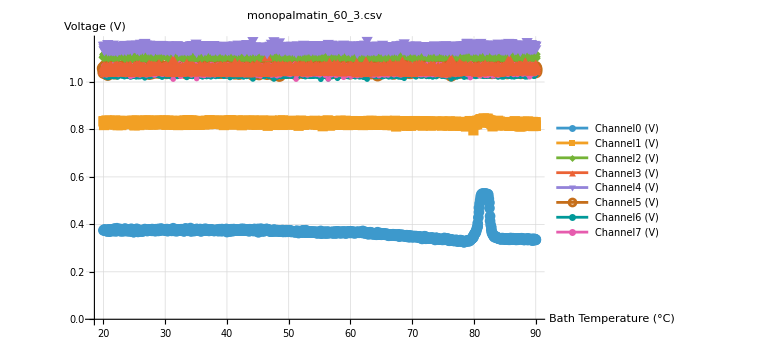

```mathematica
LabJackPlotData["monopalmatin_60_3.csv"]
```

```mathematica
LabJackRecordData["monopalmatin_60_2",90,3]
```

Recorded 955 readings over 3158 s -- saved to C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_60_2.csv

C:\Users\Student\Desktop\machine_controller\MachineControl\v2\data\monopalmatin_60_2.csv

```mathematica
LabJackListCSVs[]
```